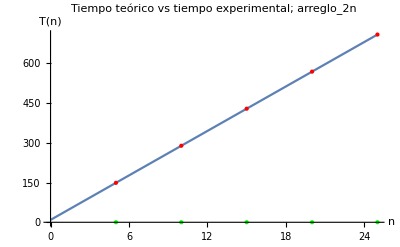

```mathematica
f[n_]:=28*n+9;
funcionFactorial=Plot[f[n],{n,0,25}];
puntos={{5,f[5]},{10,f[10]},{15,f[15]},{20, f[20]},{25, f[25]}};
graficaPuntos=ListPlot[puntos,PlotStyle->{PointSize[Large],Red},AxesLabel->{"Eje X","Eje Y"},PlotRange->All];
puntosNano={{5,0.130577},{10, 0.166152},{15,0.116416},{20, 0.114532},{25,0.120463 }};
graficaPuntosNano=ListPlot[puntosNano,PlotStyle->{PointSize[Large],Green},AxesLabel->{"n","T(n)"},PlotRange->All];
Show[funcionFactorial,graficaPuntos,graficaPuntosNano, PlotRange->All,PlotLabel->"Tiempo teórico vs tiempo experimental; arreglo_2n", 
AxesLabel->{"n","T(n)"}]
```

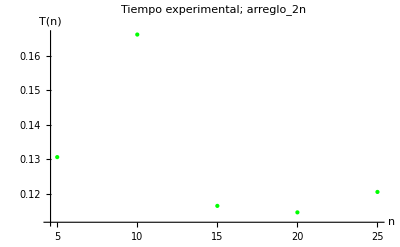

```mathematica
puntosNano={{5,0.130577},{10, 0.166152},{15,0.116416},{20, 0.114532},{25,0.120463 }};
graficaPuntosNano=ListPlot[puntosNano,PlotStyle->{PointSize[Large],Green},AxesLabel->{"n","T(n)"},PlotRange->All, PlotLabel->"Tiempo experimental; arreglo_2n"]
```